```mathematica
(*w=1*)
q[v_]:=0.5*Erfc[v/(√2)];
g2[b_, la_, k_]:=-(b+la+2k)/(√(2. π))Exp[(-(b-la)^2)/2.]+(b+k)/(√(2π))Exp[(-(b+k)^2)/2.]+0.5*((b+k)^2+1)(Erf[(b+k)/(√2)]-Erf[(b-la)/(√2)]);
(*Int*)
g2Int[b_, k_, nd_, ndR_]:=NIntegrate[Exp[-x^2/2]/(√(2.π))(k+b-x)^2 Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
f[b_, la_, k_, ns_, t_]:=Exp[(-g2 [b, la, k]t)/(2.  ns)];
fInt[b_, k_, nd_, ndR_, ns_, t_]:=Exp[(-g2Int[b, k, nd, ndR]t)/(2.  ns)];
puu0[u_, u0_, f_]:=Sqrt[1/(2. π (1-f^2))]Exp[(-(u-u0 f)^2)/(2(1-f^2))];
(***************************************************************************************************************************)
(*z=ReLU(u-b)*)
(*expectation value of z with initial overlap u0*)
expzu0[b_, f_, u0_]:=(ⅇ^((-(b- u0 f)^2)/(2 (1-f^2))) √(1-f^2))/(√(2. π))-0.5(b-u0 f) Erfc[(b-u0 f)/(√(2(1-f^2)))];
(*expectation value of z^2 with initial overlap u0*)
expz2u0[b_, f_, u0_]:=(ⅇ^((-(b-u0 f)^2)/(2 (1-f^2))) √(1-f^2) (-b+u0 f))/(√(2. π))+0.5 (1-f^2+(b-u0 f)^2) Erfc[(b-u0 f)/(√(2(1-f^2)))];
(*The probability that z is 0*)
au0[b_, f_, u0_]:= 0.5+0.5*Erf[(b-u0 f)/(√(2(1-f^2)))];
(*---------------------Part I begin-----------------------------------*)
(*Part I: average over initial overlap u0 given that the dendrite is not picked for update.*)
(* eqn (12) in note2.pdf*)
(*the dendrite with overlap v is picked for update*)
pLeftMarginI[v_, nd_, Rnd_, qv_]:=(nd  Exp[-v^2/2])/(√(2 π))(1-qv)^(nd-1)(∏_(m=1)^(Rnd-1) qv/(1-qv)*(nd-m)/(Rnd -m));(*qv should always be q[v]*)
(*the dendrite with overlap v is not picked for update*)
pLeftMarginII[v_, nd_, Rnd_, qv_]:=(nd  Exp[-v^2/2])/(√(2 π))(1-qv)^(nd-1)(∏_(m=1)^Rnd qv/(1-qv)*(nd-m)/(Rnd -m+1));(*qv should always be q[v]*)
(*averge of E[z], z≠ReLU(v-b) *)
expzI[b_, f_, nd_, ndR_]:=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expzu0[b, f, u0], {v, -Infinity, Infinity}, {u0, -Infinity, v}];
(*averge of E[Subscript[Y, I]]*)
expYI[b_, f_, nd_, ndR_]:=(nd-ndR)expzI[b, f, nd, ndR];

(*averge of E[z^2], z≠ReLU(v-b) *)
expz2I[b_, f_, nd_, ndR_]:=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expz2u0[b, f, u0], {v, -Infinity, Infinity}, {u0, -Infinity, v}];
(*averge of E[Subscript[z, 1] Subscript[z, 2]], Subscript[z, 1],Subscript[z, 2]≠ReLU(v-b) *)
(*expzzI[b_, f_, nd_, ndR_]:=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]]/(1-q[v])^2 NIntegrate[Exp[-u0^2/2.]/(√(2π))expz2u0[b, f, u0], {u0, -Infinity, v}]^2, {v, -Infinity, Infinity}];*)
expzzI[b_, f_, nd_, ndR_]:=(nd (nd-1))/((nd-ndR)(nd-ndR-1))NIntegrate[ NIntegrate[expzu0[b, f, √2. InverseErfc[2 qu0]], {qu0, InverseBetaRegularized[x, ndR, nd-ndR-1], 1}]^2, {x, 0, 1}];
(*averge of E[Subscript[Y, I]^2]*)
expY2I[b_, f_, nd_, ndR_]:=(nd-ndR)(nd-ndR-1)expzzI[b, f, nd, ndR]+ (nd-ndR)expz2I[b, f, nd, ndR];
(*AI[b_, f_, nd_, ndR_]:=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]]/(1-q[v])^(nd-ndR) NIntegrate[Exp[-u0^2/2.]/(√(2π))au0[b, f, u0], {u0, -Infinity, v}]^(nd-ndR), {v, -Infinity, Infinity}];*)
AI[b_, f_, nd_, ndR_]:=nd Binomial[nd-1, ndR-1] NIntegrate[x^(ndR-1)NIntegrate[au0[b, f, √2. InverseErfc[2 qu0]],{qu0, x, 1}]^(nd-ndR), {x, 0, 1}];
(*---------------------Part I end-----------------------------------*)


(*---------------------Part II begin-----------------------------------*)
(*expectation value of z and z^2 given that the dendrite is updated at t=0. 
Note: for simplicity,    we do not consider the possibility that a dendrite is picked for update but not updated because its overlap is already above b+k*)
expzII[b_, f_, k_, ns_, nd_, ndR_]:=expzu0[b, f, b+k];
expz2II[b_, f_, k_, ns_, nd_, ndR_]:=expz2u0[b, f, b+k];
aII[b_, f_, k_, ns_, nd_, ndR_]:=au0[b, f, b+k];
(*same as above, but condider the possibility that .......*)
(*averge of E[z], z≠ReLU(v-b) *)
expzII[b_, f_, k_, ns_, nd_, ndR_]:=NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expzu0[b, f, (b+k)/(√(1+((b+k)^2-u0^2)/ns))], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expzu0[b, f, u0], {u0, b+k, Infinity}];
(*averge of E[Subscript[Y, II]]*)
expYII[b_, f_, k_, ns_, nd_, ndR_]:=ndR expzII[b, f, k, ns, nd, ndR];
(*averge of E[z^2], z≠ReLU(v-b) *)
expz2II[b_, f_, k_, ns_, nd_, ndR_]:=NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expz2u0[b, f, (b+k)/(√(1+((b+k)^2-u0^2)/ns))], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expz2u0[b, f, u0], {u0, b+k, Infinity}];
tmpFun[b_, k_, ns_, u0_]:=(b+k)/(√(1+((b+k)^2-u0^2)/ns));
(*averge of E[Subscript[z, 1] Subscript[z, 2]], Subscript[z, 1],Subscript[z, 2]≠ReLU(v-b) *)
expzzII[b_, f_, k_, ns_, nd_, ndR_]:=(nd (nd-1))/(ndR(ndR-1))NIntegrate[(NIntegrate[expzu0[b, f, tmpFun[b, k, ns, √2. InverseErfc[2 qu0]]], {qu0,q[b+k], InverseBetaRegularized[x, ndR-1, nd-ndR]}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expzu0[b, f, u0], {u0, b+k, Infinity}])^2, {x, BetaRegularized[q[(b+k)], ndR-1, nd-ndR], 1} ];
(*averge of E[Subscript[Y, II]^2]*)
expY2II[b_, f_, k_, ns_, nd_, ndR_]:=ndR(ndR-1)expzzII[b, f, k, ns, nd, ndR]+ ndR expz2II[b, f, k, ns, nd, ndR];
AII[b_, f_, k_, ns_, nd_, ndR_]:=nd Binomial[nd-1, ndR]NIntegrate[(1-x)^(ns-ndR-1)(NIntegrate[au0[b, f, tmpFun[b, k, ns, √2. InverseErfc[2 qu0]]], {qu0,q[b+k], x}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)au0[b, f, u0], {u0, b+k, Infinity}])^ndR,{x, BetaRegularized[q[(b+k)], ndR-1, nd-ndR], 1}];

(*---------------------Part II end-----------------------------------*)
(***************************************************************************************************************************)
(* Y=∑_(i=1)^n zi, logA=∑_(i=1)^n loga *)
(*expYI[b_, f_, nd_, ndR_]:=(nd-ndR)expzI[b, f, nd, ndR];
expY2I[b_, f_, nd_, ndR_]:=(nd-ndR)(nd-ndR-1)expzI[b, f, nd, ndR]^2 + (nd-ndR)expz2I[b, f, nd, ndR];
AI[b_, f_, nd_, ndR_]:=aI[b, f, nd, ndR]^(nd-ndR);
expYII[b_, f_, k_, ns_, nd_, ndR_]:=ndR expzII[b, f, k, ns, nd, ndR];
expY2II[b_, f_, k_, ns_, nd_, ndR_]:=ndR(ndR-1)expzII[b, f, k, ns, nd, ndR]^2+ ndR expz2II[b, f, k, ns, nd, ndR];
AII[b_, f_, k_, ns_, nd_, ndR_]:=aII[b, f, k, ns, nd, ndR]^ndR;*)
expYSteady[b_, nd_, ndR_]:=nd expzI[b, 0., nd, ndR];
expY2Steady[b_, nd_, ndR_]:=nd(nd-1)expzI[b, 0., nd, ndR]^2 + nd expz2I[b, 0., nd, ndR];
ASteady[b_, nd_, ndR_]:=au0[b, 0., 0.]^nd;
(***************************************************************************************************************************)
(*The ansatz of P(Y) is P(Y)=Aδ(Y)+(1-A)/(√(π/2)σ(1+Erf[μ/(√2 σ)]))Exp[(-(Y-μ)^2)/(2 σ^2)]θ(Y). 
μ and σ can be obtained from the following two equations: 
E[Y]/σ=(1-A)h[μ/σ];  E[Y^2]/σ^2=(1-A)(1+μ/σ h[μ/σ]). 
h[x] is defined below. 
*)
h[x_]:=x+Exp[-x^2/2.]/(√(π/2.)(1+Erf[x/(√2)]));
ansatzMuOverSigma[expY_, expY2_, A_]:=x/.FindRoot[((1-A)expY2)/expY^2 h[x]^2==1+x h[x], {x, 100.}];
ansatzSigma[expY_, expY2_, A_, muOverSigma_]:=expY/((1-A)h[muOverSigma]);
ansatzMu[muOverSigma_, sigma_]:=muOverSigma*sigma;
ansatzProbY[Y_, mu_, sigma_, A_]:=A DiracDelta[Y] + (1-A)/(√(π/2)sigma(1+Erf[mu/(√2 sigma)]))Exp[(-(Y-mu)^2)/(2 sigma^2)]HeavisideTheta[Y];
probY[Y_, muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=1.*AI*AII DiracDelta[Y] + (AI(1-AII))/(√(π/2)sigmaII(1+Erf[muII/(√2 sigmaII)]))Exp[(-(Y-muII)^2)/(2 sigmaII^2)]HeavisideTheta[Y]+ (AII(1-AI))/(√(π/2)sigmaI(1+Erf[muI/(√2 sigmaI)]))Exp[(-(Y-muI)^2)/(2 sigmaI^2)]HeavisideTheta[Y]+((1-AI)(1-AII)ⅇ^(-(muI+muII-Y)^2/(2 (sigmaI^2+sigmaII^2))))/(√(π/2)√(sigmaI^2+sigmaII^2))(Erf[(muII sigmaI^2+sigmaII^2 (-muI+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]+Erf[(muI sigmaII^2+sigmaI^2 (-muII+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))])/((1+Erf[muI/(√2 sigmaI)])(1+Erf[muII/(√2 sigmaII)]));
falseNegative[th_, muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=1-(AI(1-AII)(1+Erf[(muII-th)/(√2 sigmaII)]))/(1+Erf[muII/(√2 sigmaII)])-(AII(1-AI)(1+Erf[(muI-th)/(√2 sigmaI)]))/(1+Erf[muI/(√2 sigmaI)])-((1-AI)(1-AII))/(√(π/2)√(sigmaI^2+sigmaII^2)(1+Erf[muI/(√2 sigmaI)])(1+Erf[muII/(√2 sigmaII)]))NIntegrate[ⅇ^(-(muI+muII-Y)^2/(2 (sigmaI^2+sigmaII^2)))(Erf[(muII sigmaI^2+sigmaII^2 (-muI+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]+Erf[(muI sigmaII^2+sigmaI^2 (-muII+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]), {Y, th, Infinity}];
Y99Lower[muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=If[AI AII>=0.01, 0, th/.FindRoot[falseNegative[th, muI, sigmaI, AI, muII, sigmaII, AII]==0.01, {th, 0, b+k}, Method->"Brent"]];
Y99Upper[muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=th/.FindRoot[falseNegative[th, muI, sigmaI, AI, muII, sigmaII, AII]==0.99, {th, 0, 5*(b+k)}, Method->"Brent"];
YMean[muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=AI (1.-AII) (muII-(ⅇ^(-muII^2/(2 sigmaII^2)) √(2/π) sigmaII)/(-2+Erfc[muII/(√2 sigmaII)]))+ AII(1.-AI) (muI-(ⅇ^(-muI^2/(2 sigmaI^2)) √(2/π) sigmaI)/(-2+Erfc[muI/(√2 sigmaI)]))+((1-AI)(1-AII))/(√(π/2)√(sigmaI^2+sigmaII^2))1./((1+Erf[muI/(√2 sigmaI)])(1+Erf[muII/(√2 sigmaII)]))NIntegrate[ⅇ^(-(muI+muII-Y)^2/(2 (sigmaI^2+sigmaII^2)))(Erf[(muII sigmaI^2+sigmaII^2 (-muI+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]+Erf[(muI sigmaII^2+sigmaI^2 (-muII+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))])Y, {Y, 0, Infinity}];
(***************************************************************************************************************************)
```

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

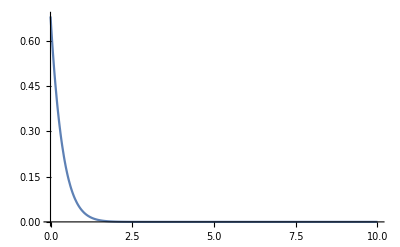

```mathematica
nd=200; ns=300; b=3.;k=5.32635-b;ndR=2;
expYSteadyVar=expYSteady[b, nd, ndR];
expY2SteadyVar=expY2Steady[b, nd, ndR];
ASteadyVar=ASteady[b, nd, ndR];
muOverSigmaSteadyVar=ansatzMuOverSigma[expYSteadyVar,expY2SteadyVar,ASteadyVar];
sigmaSteadyVar=ansatzSigma[expYSteadyVar,expY2SteadyVar,ASteadyVar, muOverSigmaSteadyVar];
muSteadyVar = ansatzMu[muOverSigmaSteadyVar, sigmaSteadyVar];
Plot[ansatzProbY[Y, muSteadyVar, sigmaSteadyVar, ASteadyVar], {Y, 0.001, 10}, PlotRange->All]
th=muSteadyVar-√2 sigmaSteadyVar InverseErf[(0.01(1+Erf[muSteadyVar/(√2 sigmaSteadyVar)]))/(1-ASteadyVar)-1];
```

```mathematica
tStart=100; tEnd=4000;tStep=200;
tList=Table[t, {t, tStart, tEnd, tStep}];
fList=Thread[fInt[b, k, nd, ndR, ns, tList]];
expYIList=Thread[expYI[b, fList, nd, ndR]];
expY2IList=Thread[expY2I[b, fList, nd, ndR]];
AIList=Thread[AI[b, fList, nd, ndR]];
expYIIList=Thread[expYII[b, fList, k, ns,nd, ndR]];
expY2IIList=Thread[expY2II[b, fList, k, ns, nd, ndR]];
AIIList=Thread[AII[b, fList, k, ns, nd, ndR]];
muOverSigmaIList=MapThread[ansatzMuOverSigma, {expYIList,expY2IList, AIList}];
sigmaIList=Thread[ansatzSigma[expYIList,expY2IList, AIList, muOverSigmaIList]];
muIList=Thread[ansatzMu[sigmaIList, muOverSigmaIList]];
muOverSigmaIIList=MapThread[ansatzMuOverSigma, {expYIIList,expY2IIList, AIIList}];
sigmaIIList=Thread[ansatzSigma[expYIIList,expY2IList, AIIList, muOverSigmaIIList]];
muIIList=Thread[ansatzMu[sigmaIIList, muOverSigmaIIList]];
falseNegativeList=Thread[falseNegative[th, muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList]];
Y99LowerList=MapThread[Y99Lower,{ muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList}];
Y99UpperList=MapThread[Y99Upper,{ muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList}];
YMeanList=MapThread[YMean,{ muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList}];
```

NIntegrate::nlim: qu0 = InverseBetaRegularized[x,2.,197.] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: qu0 = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0000565405}. NIntegrate obtained 0.0000251254 and 3.57812×10^-11 for the integral and error estimates.

NIntegrate::nlim: qu0 = InverseBetaRegularized[x,1.,198.] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: qu0 = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u0 near {u0} = {5.33829}. NIntegrate obtained 2.28113×10^-21 and 3.17692×10^-24 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-2.86989×10^-6 (-3147.88-Y)^2) (Erf[0.0000163754 (-193.628+174223. (-4.1584+Y))]+Erf[0.0000163754 (724486.+0.0614293 (3152.04+Y))]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.+th}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-2.86989×10^-6 (-3147.88-Y)^2) (Erf[0.0000163754 (-193.628+174223. (-4.1584+Y))]+Erf[0.0000163754 (724486.+0.0614293 (3152.04+Y))]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.+th}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
YMeanList
```

{4.15897,3.90299,3.6542,3.41231,3.17702,2.9483,2.72661,2.51288,2.30829,2.11402,1.93104,1.76,1.60123,1.45474,1.32029,1.19746,1.08568,0.984278,0.89255,0.809761}

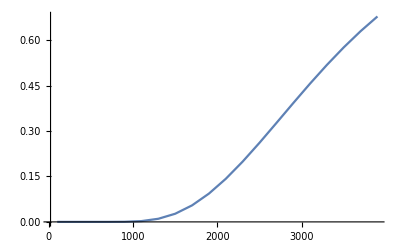

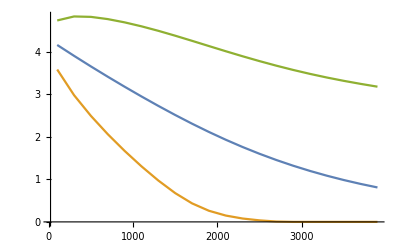

```mathematica
fnTimeList=Transpose[{tList, falseNegativeList}];
meanTimeList=Transpose[{tList, YMeanList}];
lower99TimeList = Transpose[{tList, Y99LowerList}];
upper99TimeList=Transpose[{tList, Y99UpperList}];
ListLinePlot[fnTimeList, PlotRange->All]
ListLinePlot[{meanTimeList, lower99TimeList,upper99TimeList}, PlotRange->All]
```

```mathematica
Export["meanTimeList0.csv",meanTimeList,"CSV"];
Export["lower99TimeList0.csv",lower99TimeList,"CSV"];
Export["upper99TimeList0.csv",upper99TimeList,"CSV"];
```

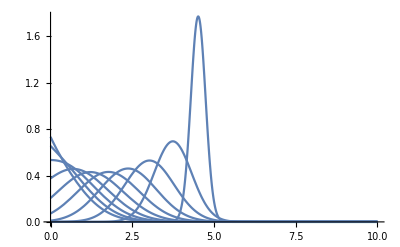

```mathematica
idx=5;
Plot[Table[probY[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]], muIIList[[idx]], sigmaIIList[[idx]], AIIList[[idx]]], {idx, 1, 30, 3}], {Y, 0, 10}, PlotRange->All]
```